# Лабораторная работа 4

## Задание

Постройте функцию CurveSecant[f, x0, x1, dx], которая отображает
заданную кривую y = f (x) и секущую по отношению к ней прямую, проходящую через точки с абсциссами x0 < x1 из области определения функции y = f (x) . Аргумент dx задает приращения x0 - dx, x1 + dx абсцисс .

```mathematica
Point[{#,f[#]}]&/@{x0,x1}
```

{Point[{x0,f[x0]}],Point[{x1,f[x1]}]}

```mathematica
Secant[f_,x0_,x1_,dx_]:=Graphics[{AbsolutePointSize[9],Hue[2/3],Point[{#,f[#]}]&/@{x0,x1}, Line[{{x0-dx, (k=(f[x1]-f[x0])/(x1-x0)) (-dx)+f[x0]}, {x1+dx, k (x1+dx - x0)}+f[x0]}]}, Axes->True, PlotRange->{{x0-dx, x1+dx},{f[x0]-dx, f[x1]+dx}}]
```

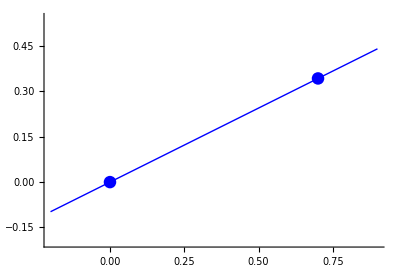

```mathematica
Secant[Power[#,3]&,0,.7,.2]
```

```mathematica
CurveSecant[f_,x0_,x1_,dx_]:=Show[Plot[f[x],{x,x0-dx, x1+dx}], Secant[f,x0,x1,dx]]
```

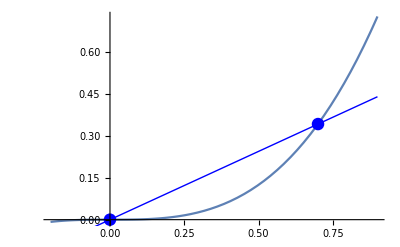

```mathematica
CurveSecant[Power[#,3]&,0,.7,.2]
```

## Задание 2

Постройте функцию, вычисляющую графическое представление замкнутой ломаной .

```mathematica
BreakLine[Counter,Verticies]
```

BreakLine[Counter,Verticies]

```mathematica
showBreakLine[BL_BrealLine]:=FunctionBody
```

```mathematica
Size=50;
```

P - список пар.

```mathematica
P=Table[{RandomInteger[Size], RandomInteger[Size]},{RandomInteger[{3,15}]}];
BL=BreakLine[Length[P],P]
```

BreakLine[5,{{23,36},{39,4},{43,36},{10,41},{6,34}}]

```mathematica
BL[[2]]
```

{{23,36},{39,4},{43,36},{10,41},{6,34}}

```mathematica
Point[#]&/@BL[[2]]
```

{Point[{23,36}],Point[{39,4}],Point[{43,36}],Point[{10,41}],Point[{6,34}]}

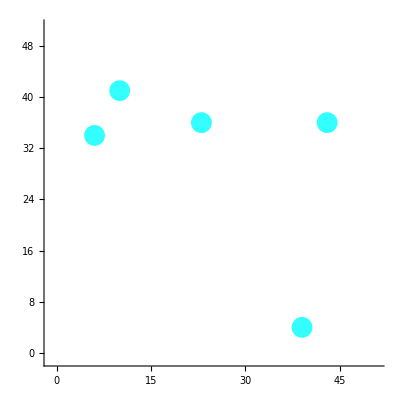

```mathematica
Fig1=Graphics[{AbsolutePointSize[15], Hue[.5,.8,1], Point[#]&/@BL[[2]]},AspectRatio->Automatic, PlotRange-> {{-1, Size+1},{-1,Size+1}},Axes->True]
```

```mathematica
{Hue[0.051],Append[BL[[2]],BL[[2,1]]]//Line}
```

{Hue[0.051],Line[{{23,36},{39,4},{43,36},{10,41},{6,34},{23,36}}]}

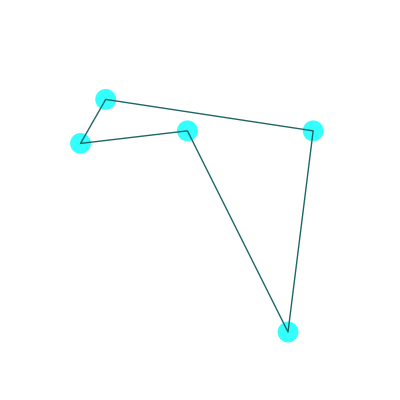

```mathematica
Fig2=Graphics[{{AbsolutePointSize[15],Hue[.5,.8,1],Point/@BL[[2]]},{Hue[.5,.7,.4],Append[BL[[2]],BL[[2,1]]]//Line}},AspectRatio->Automatic, PlotRange-> {{-1,Size+1},{-1,Size+1}}]
```

```mathematica
MapIndexed[Text[First@#2,#1]&,BL[[2]]]
```

{Text[1,{23,36}],Text[2,{39,4}],Text[3,{43,36}],Text[4,{10,41}],Text[5,{6,34}]}

```mathematica
MapIndexed[{{Point[#1]},Text[First@#2,#1]}&,BL[[2]]]
```

{{{Point[{23,36}]},Text[1,{23,36}]},{{Point[{39,4}]},Text[2,{39,4}]},{{Point[{43,36}]},Text[3,{43,36}]},{{Point[{10,41}]},Text[4,{10,41}]},{{Point[{6,34}]},Text[5,{6,34}]}}

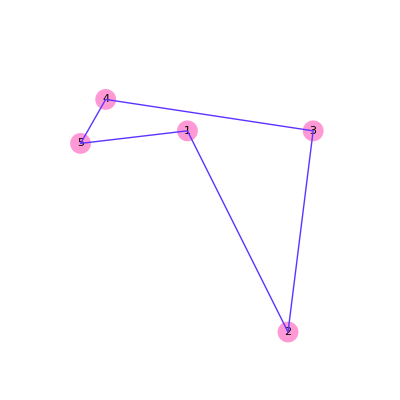

```mathematica
Fig3=Graphics[{AbsolutePointSize[15],MapIndexed[{{Hue[.9,.4,1],Point[#1]},Text[First@#2,#1]}&,BL[[2]]],Hue[.7,.8,1],Append[BL[[2]],BL[[2,1]]]//Line}, AspectRatio->Automatic, PlotRange->{{-1,Size+1},{-1,Size+1}}]
```

```mathematica
ClearAll[showBreakLine]
showBreakLine[BL_BreakLine]:=Graphics[{AbsolutePointSize[15],Hue[.9,.4,.1],Point[#]&/@BL[[2]],Hue[.7,.8,1],Line[Append[BL[[2]],BL[[2,1]]]],MapIndexed[{Text[First@#2,#1]}&,BL[[2]]]},AspectRatio->Automatic,Axes->True,PlotRange->{{-1, Max[Table[BL[[2,i,1]], {i,1,Length[BL[[2]]]}]]+1},{-1, Max[Table[BL[[2,i,2]], {i,1,Length[BL[[2]]]}]]+1}}]
```

## Задание 3

### 1)

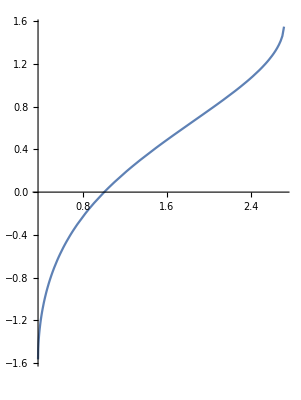

```mathematica
ParametricPlot[{ⅇ^t, ArcSin[t]},{t, -10,10}]
```

### 2)

```mathematica
ParPoint[n_]:=Table[{ⅇ^t, ArcSin[t]},{t, RandomReal[{0,8},n]}]
```

```mathematica
T=ParPoint[7]
```

{{2.62937,1.31218},{2946.93,1.5708-2.76721 ⅈ},{926.174,1.5708-2.60923 ⅈ},{2119.43,1.5708-2.72473 ⅈ},{60.2924,1.5708-2.08872 ⅈ},{514.471,1.5708-2.51815 ⅈ},{19.3219,1.5708-1.74894 ⅈ}}

### 3)

```mathematica
Show[Graphics
```